```mathematica
(* RUN transientQBD_functions.nb FIRST !!!! *)

(* QBD model of a TDM voice/data packets integration
strategy*)
Tinfinite={0,1};
K = 2;

F=ConstantArray[0,K];
B=ConstantArray[0,K];
L=ConstantArray[0,K];
Lv=ConstantArray[0,K+1];
lamda1=0.1;
lamda2=0.1;
mu1=0.5;
mu2=0.5;
a1=-lamda1-lamda2;
a2=-lamda1-lamda2-mu1;
a3=-lamda1-lamda2-2mu1;
a4=-lamda1-lamda2-3mu1;
a5=-lamda1-lamda2-4mu1;
a6=-lamda2-5mu1;
Lv[[1]]=({{a1, lamda1, 0, 0, 0, 0}, {mu1, a2, lamda1, 0, 0, 0}, {0, 2mu1, a3, lamda1, 0, 0}, {0, 0, 3mu1, a4, lamda1, 0}, {0, 0, 0, 4mu1, a5, lamda1}, {0, 0, 0, 0, 5mu1, a6}});
F[[1]]=lamda2*IdentityMatrix[6];
B[[1]]=({{mu2, 0, 0, 0, 0, 0}, {0, mu2, 0, 0, 0, 0}, {0, 0, mu2, 0, 0, 0}, {0, 0, 0, mu2, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}});
b1=-lamda1-lamda2-mu2;
b2=-lamda1-lamda2-mu1-mu2;
b3=-lamda1-lamda2-2*mu1-mu2;
b4=-lamda2-3*mu1-mu2;
b5=-lamda1-lamda2-4*mu1;
b6=-lamda2-5*mu1;
Lv[[2]]=({{b1, lamda1, 0, 0, 0, 0}, {mu1, b2, lamda1, 0, 0, 0}, {0, 2mu1, b3, lamda1, 0, 0}, {0, 0, 3mu1, b4, 0, 0}, {0, 0, 0, 4mu1, b5, lamda1}, {0, 0, 0, 0, 5mu1, b6}});
c1=-lamda1-lamda2-2*mu2;
c2=-lamda2-mu1-2*mu2;
c3=-lamda1-lamda2-2*mu1-mu2;
c4=-lamda2-3*mu1-mu2;
c5=-lamda1-lamda2-4*mu1;
c6=-lamda2-5*mu1;
L[[2]]=({{c1, lamda1, 0, 0, 0, 0}, {mu1, c2, 0, 0, 0, 0}, {0, 2mu1, c3, lamda1, 0, 0}, {0, 0, 3mu1, c4, 0, 0}, {0, 0, 0, 4mu1, c5, lamda1}, {0, 0, 0, 0, 5mu1, c6}});
B[[2]]=({{2mu2, 0, 0, 0, 0, 0}, {0, 2mu2, 0, 0, 0, 0}, {0, 0, mu2, 0, 0, 0}, {0, 0, 0, mu2, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}});
F[[2]]=F[[1]];
(*Lv[[3]]=L[[2]]+F[[2]];
Total[BuildBig[F,L,B,Lv,Tfinite],{2}]//Chop*)
```

```mathematica
(Lv[[1]]+F[[1]]).Table[1,{6}]//Chop
(B[[1]]+Lv[[2]]+F[[2]]).Table[1,{6}]//Chop
(B[[2]]+L[[2]]+F[[2]]).Table[1,{6}]//Chop
```

{0,0,0,0,0,0}

{0,0,0,0,0,0}

{0,0,0,0,0,0}

```mathematica
PB[ V_,t_]:=Module[{ii,res,res0,res1,res2,res3,fres0,fres1,fres2,fres3,frestotP,e1,e1T,e13T,e135T,linexx},
e1={1 , 0, 0,0,0,0};
e1T={0 , 0, 0,0,0,1};
e13T={0,0 ,0,1,0,1};
e135T={0,1,0,1,0,1};
linexx=ConstantArray[0,Length[V]];
For[ii=1,ii<=Length[V],ii++,
res0= ILT[Function[s,Transient2Open[B,L,F,Lv,Tinfinite,V[[ii]],0,s]],Range[1/10,t,1/5], 35];
res1= ILT[Function[s,Transient2Open[B,L,F,Lv,Tinfinite,V[[ii]],1,s]],Range[1/10,t,1/5], 35];
res2= Sum[ILT[Function[s,Transient2Open[B,L,F,Lv,Tinfinite,V[[ii]],j,s]],Range[1/10,t,1/5], 35],{j,2,V[[ii]]-1}];
res3= ILT[Function[s,Transient2Open[B,L,F,Lv,Tinfinite,V[[ii]],V[[ii]],s].Inverse[IdentityMatrix[Length[L[[K]]]]-QBDFundamentalMatrices[B[[K]],L[[K]]-s IdentityMatrix[Length[L[[K]]]],F[[K]],"GR"][[2]]]
],Range[1/10,t,1/5], 35];
fres0=Table[e1.res0[[i,;;,;;]].e1T,{i,1,Dimensions[res0][[1]]}];(*V(t,n,0)*)
fres1=Table[e1.res1[[i,;;,;;]].e13T,{i,1,Dimensions[res1][[1]]}];
fres2=Table[e1.res2[[i,;;,;;]].e135T,{i,1,Dimensions[res2][[1]]}];
fres3=Table[e1.res3[[i,;;,;;]].e135T,{i,1,Dimensions[res3][[1]]}];
frestotP=fres0+fres1+fres2+fres3;
linexx[[ii]]=Transpose[{Range[1/10,t,1/5],frestotP}];

];
Return[linexx];
];
```

```mathematica
n={3,19,31};
t=40;
PBALL=PB[n,t];
```

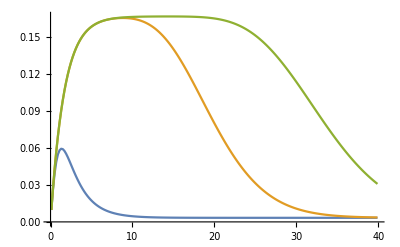

```mathematica
ListLinePlot[PBALL,PlotRange->All]
```

```mathematica
NV[ V_,t_]:=Module[{ii,res1,res2,fres1,fres2,frestotP,e1,e16T,linexx},
e1={1 , 0, 0,0,0,0};
e16T={0,1,2,3,4,5};
linexx=ConstantArray[0,Length[V]];
For[ii=1,ii<=Length[V],ii++,

res1= Sum[ILT[Function[s,Transient2Open[B,L,F,Lv,Tinfinite,V[[ii]],j,s]],Range[1/10,t,1/5], 35],{j,0,V[[ii]]-1}];
res2= ILT[Function[s,Transient2Open[B,L,F,Lv,Tinfinite,V[[ii]],V[[ii]],s].Inverse[IdentityMatrix[Length[L[[K]]]]-QBDFundamentalMatrices[B[[K]],L[[K]]-s IdentityMatrix[Length[L[[K]]]],F[[K]],"GR"][[2]]]
],Range[1/10,t,1/5], 35];

fres1=Table[e1.res1[[i,;;,;;]].e16T,{i,1,Dimensions[res1][[1]]}];
fres2=Table[e1.res2[[i,;;,;;]].e16T,{i,1,Dimensions[res2][[1]]}];
frestotP=fres1+fres2;
linexx[[ii]]=Transpose[{Range[1/10,t,1/5],frestotP}];

];
Return[linexx];
];
```

```mathematica
n={3,19,31};
t=40;
NVALL=NV[n,t];
```

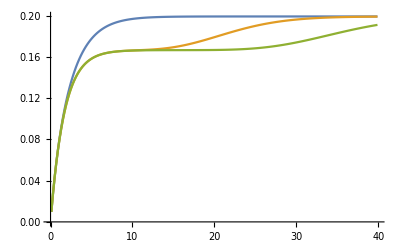

```mathematica
ListLinePlot[NVALL,PlotRange->All]
```

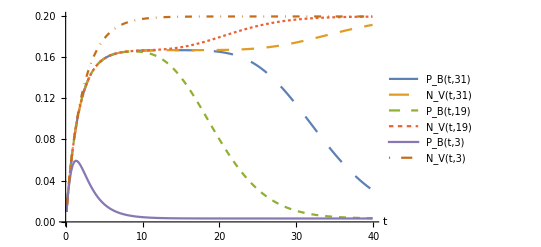

```mathematica
ListLinePlot[{PBALL[[3]],NVALL[[3]],PBALL[[2]],NVALL[[2]],PBALL[[1]],NVALL[[1]]},PlotRange->All,PlotLegends->{"P_B(t,31)","N_V(t,31)", "P_B(t,19)","N_V(t,19)","P_B(t,3)","N_V(t,3)"},AxesLabel->{"t"},PlotStyle -> { Dashing[Large],Dashing[Medium],Dashing[Small],Dashing[Tiny] ,Line,DotDashed}]
```